Calculation of the Logistic Map

```mathematica
f[r_]:=NestList[1-r#^2&,.01,1000][[-100;;]]
ListPlot[Flatten[Table[{r,#}&/@f[r],{r,0,2,1/1000}],1]]
```

-Graphics-

(r==0&&x==1)||(r≠0&&(x==(-1-√(1+4 r))/(2 r)||x==(-1+√(1+4 r))/(2 r)))

(r==0&&x==1)||(r≠0&&(x==(r-r √(-3+4 r))/(2 r^2)||x==(r+r √(-3+4 r))/(2 r^2)))||(r≠0&&(x==(-1-√(1+4 r))/(2 r)||x==(-1+√(1+4 r))/(2 r)))

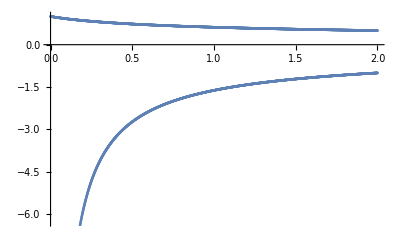

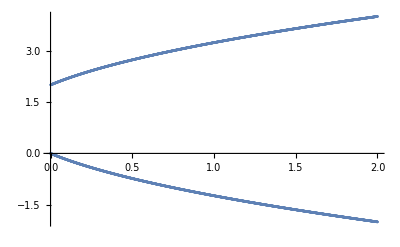

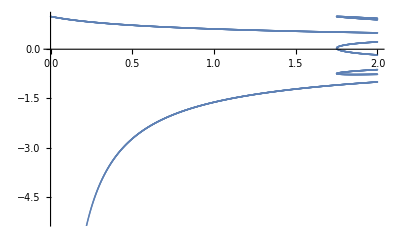

```mathematica
Reduce[1-r*x^2==x,x]
Reduce[1-r(1-r*x^2)^2==x,x]
f1[r_]:=Flatten[List[x/.Solve[1-r*x^2==x,x]]]
f2[r_]:=Flatten[List[x/.Solve[1-r(1-r(1-r*x^2)^2)^2==x,x]]]
g1:=Flatten[Table[{r,#}&/@f1[r],{r,0,2,1/1000}],1]
g2:=Flatten[Table[{r,-2r*#}&/@f1[r],{r,0,2,1/1000}],1]
g3:=Flatten[Table[{r,#}&/@f2[r],{r,0,2,1/1000}],1]
ListPlot[g1]
ListPlot[g2]
ListPlot[g3]
```

Calculation of the Lyapunov exponent for the Logistic Map

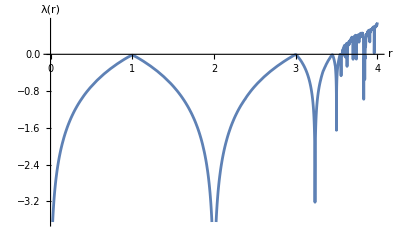

```mathematica
λ[r_]:=Module[{f,μ},f[x_]:=r x (1-x);
μ[x_]:=Log[Abs[r (1-2 x)]];
Mean[μ[NestList[f,0.3,500]]]];
Plot[λ[r],{r,0,4},PlotStyle->Thickness[.005],AxesLabel->{"r","λ(r)"}]
```

```mathematica
f[r_]:=NestList[r*#(1-#)&,.01,1000][[-100;;]]
ListPlot[Flatten[Table[{r,#}&/@f[r],{r,0,4,1/1000}],1]]
```

-Graphics-